General Tools

```mathematica
Needs["Fretica`"]
```

### Global Fitting: FFindGlobalFit

```mathematica
?FFindGlobalFit
```

FFindGlobalFit[ {dat1,dat2,...}, {model1,model2,...}, pars, vars ] or
FFindGlobalFit[ {dat1,dat2,...}, {model1,model2,...}, constraints, pars,vars ]
allow to fit several data sets simultaneously with shared (and individual) model parameters. pars is a list of the fit parameters paired with initial guess values of the form pars=={{par1,val1},{par1,val2},...}
The rest is identical to FindFit.
All Options of FindFit can be used for FindGlobalFit.

#### Some data

Two noisy data sets of oscillations with same frequency but different amplitudes (and phases) :

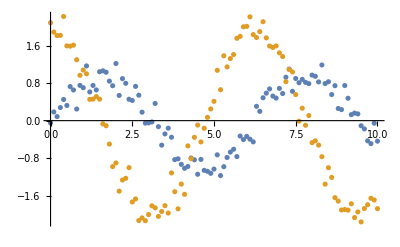

```mathematica
dat1=Table[{t,Sin[ω t]+RandomReal[NormalDistribution[0,0.2]]/.ω->1},{t,0,10,0.1}];
dat2=Table[{t,2 Cos[ω t]+RandomReal[NormalDistribution[0,0.2]]/.ω->1},{t,0,10,0.1}];
ListPlot[{dat1,dat2}]
```

#### Unconstrained global fit:

```mathematica
data={dat1,dat2};
model={a[1] Sin[ω t],a[2] Cos[ω t]};
guess={{ω,0.7},{a[1],0.77},{a[2],1.}};
fitresult=FFindGlobalFit[data,model,guess,{t}]
Show[ListPlot[data],Plot[model/.fitresult,{t,0,10}]]
```

{ω→1.00296,a[1]→0.97253,a[2]→1.98031}

-Graphics-

#### Constrained global fit:

```mathematica
data={dat1,dat2};
model={a[1] Sin[ω t],a[2] Cos[ω t]};
guess={{ω,0.7},{a[1],0.77},{a[2],1.}};
fitresult=FFindGlobalFit[data,model,{ω<0.9,a[1]<=a[2]},guess,{t}]
Show[ListPlot[data],Plot[model/.fitresult,{t,0,10}]]
```

{ω→0.9,a[1]→0.773586,a[2]→1.73934}

-Graphics-

### Global Fitting: FNonlinearModelGlobalFit

```mathematica
?FNonlinearModelGlobalFit
```

FNonlinearModelGlobalFit[ {dat1, dat2,...}, {model1, model2,...}, pars, vars ] or
FNonlinearModelGlobalFit[ {dat1, dat2,...}, {model1, model2,...}, constraints, pars, vars ]
pars is a list of the fit parameters paired with initial guess values of the form pars=={{par1, val1},{par2,val2},...}
The rest is identical to NonlinearModelFit.
All Options of NonlinearModelFit can be passed to FNonlinearModelGlobalFit.

#### Some data

Two noisy data sets of ocillations with the same frequency but different amplitudes (and phases) :

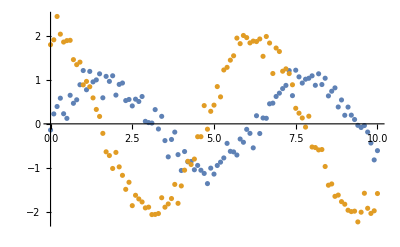

```mathematica
dat1=Table[{t,Sin[ω t]+RandomReal[NormalDistribution[0,0.2]]/.ω->1},{t,0,10,0.1}];
dat2=Table[{t,2 Cos[ω t]+RandomReal[NormalDistribution[0,0.2]]/.ω->1},{t,0,10,0.1}];
ListPlot[{dat1,dat2}]
```

#### Unconstrained global fit:

```mathematica
data={dat1,dat2};
model={a[1] Sin[ω t],a[2] Cos[ω t]};
guess={{ω,0.7},{a[1],0.77},{a[2],1.}};
fit=FNonlinearModelGlobalFit[data,model,guess,{t}]
fit["BestFitParameters"]
Show[ListPlot[data],Plot[{fit[1,t],fit[2,t]},{t,0,10}],Frame->True]
```

FittedModel[Fretica`Private`gm$83392[Fretica`Private`n$83392][{t},{1.00232,1.02141,2.00813}]]

{ω→1.00232,a[1]→1.02141,a[2]→2.00813}

-Graphics-

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 1.00232 | 0.00208408 | 480.939 | 5.18737×10^-307
a[1] | 1.02141 | 0.0266814 | 38.2818 | 9.94594×10^-94
a[2] | 2.00813 | 0.0253162 | 79.322 | 1.47795×10^-152

#### Constrained global fit:

```mathematica
data={dat1,dat2};
model={a[1] Sin[ω t],a[2] Cos[ω t]};
guess={{ω,0.7},{a[1],0.77},{a[2],1.}};
fit=FNonlinearModelGlobalFit[data,model,{ω<0.9,a[1]<=a[2]},guess,{t}]
fit["BestFitParameters"]
Show[ListPlot[data],Plot[{fit[1,t],fit[2,t]},{t,0,10}],Frame->True]
```

FittedModel[Fretica`Private`gm$84660[Fretica`Private`n$84660][{t},{0.9,0.81051,1.76845}]]

{ω→0.9,a[1]→0.81051,a[2]→1.76845}

-Graphics-

### Reading curve data from a plot-image

```mathematica
?FReadCoordinatesFromImage
```

FReadCoordinatesFromImage[outputcurve,diagramimage] opens interactive control for reading coordinates from an image (e.g. a scanned plot from a publication). The coordinates are stored in outputcurve, which must be a valid variable name.

Operation sequence

1. Enter the reference points at the plot x axes into the input fields.
2. Alt + Click on the point with x - coordinate x1. This brings up the first locator visible as a circle. Alt + Click (Command + Click for Mac OS X) on that with x2 which gives rise to the second locator. Adjust the locators, if necessary. Press the button " Set x scale".
3. Enter the reference points at the plot y axes into the input fields. Press Enter. Move the two already existing locators to the points with the coordinates y1 and y2. Press the button " Set y scale ". Now the both scales are captured.
4. Move the two already existing locators to the first two points of the curve to be captured. Alt + Click on other points of the curve. Each Alt + Click will generate an additional locator. Adjust locators, if necessary. To remove, press Alt + Click on unnecessary locators.
5. Press the button " Update ' curvedat' ". This assigns the captured list to the global variable listOfPoints. Done.
   
 (Adapted from ' copyCurve' of Alexei Boulbitch published at mathematica.stackexchange.com)

```mathematica
pic=-Graphics-;
```

```mathematica
FReadCoordinatesFromImage[curvedat,pic]
```

```mathematica
PEDetectionEfficiency=Interpolation[curvedat]
```

InterpolatingFunction[…]

```mathematica
curvedat
```

{{401.445,7.77},{502.254,48.423},{556.593,59.96},{627.927,69.744},{685.278,73.001},{742.66,70.49},{786.057,65.977},{835.662,53.681},{875.986,44.159},{996.927,15.814}}

InterpolatingFunction::dmval: Input value {400.012} lies outside the range of data in the interpolating function. Extrapolation will be used.

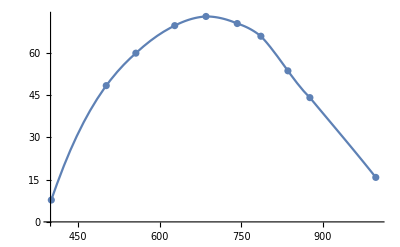

```mathematica
Show[Plot[PEDetectionEfficiency[λ],{λ,400,1000}],
ListPlot[curvedat]]
```

### FPowerSpectrum

```mathematica
?FPowerSpectrum
```

FPowerSpectrum[xydat_,firstν  _] or FPowerSpectrum[xydat_]

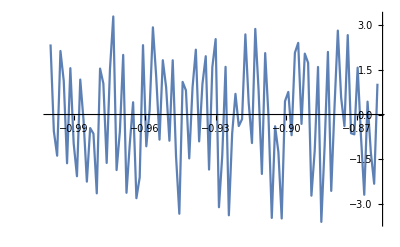

-Graphics-

```mathematica
dat=Table[{t,Sin[2π 50 t]+2Cos[2π 230 t]+1RandomReal[{-1,1}]},{t,-1,1,0.0014}];
ListPlot[dat[[1;;100]],PlotRange->All,Joined->True]
ListLogPlot[FPowerSpectrum[dat],PlotRange->All,Frame->True,Joined->True]
```

| Related Guides
▪Fretica